## 方孔的夫琅禾费衍射

夫琅禾费衍射的振幅是输入振幅的傅里叶积分变换乘以球面波因子和1/iλ ，以下公式省去这些因子，得出的是相对振幅和强度。

对于方孔来说，入射面的振幅积分可以写成方孔区域的积分。

```mathematica
Hold[Integrate[Exp[-I k (l x1 + m y1)], {x1, -a/2, a/2}, {y1, -b/2, b/2}]]//TraditionalForm
```

Hold[∫_(-a/2)^(a/2) ∫_(-b/2)^(b/2) exp(-ⅈ k (l x1+m y1))ⅆy1ⅆx1]

```mathematica
Exy = Integrate[Exp[-I k (l x1 + m y1)], {x1, -a/2, a/2}, {y1, -b/2, b/2}]
```

(4 Sin[(a k l)/2] Sin[(b k m)/2])/(k^2 l m)

对于

```mathematica
Ex=Limit[Exy ,m-> 0]
```

(2 b Sin[(a k l)/2])/(k l)

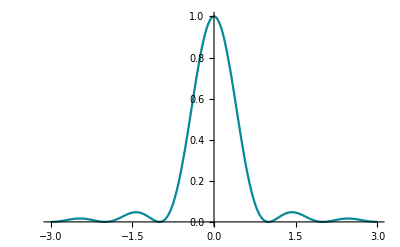

```mathematica
Plot[Abs[Ex]^2/.{a-> 1,k-> 2 π,b-> 1},{l,-3,3}]
```

```mathematica
Simplify[D[Ex^2 /. {b -> 1, k -> 2 π, a -> 1}, l] == 0,Assumptions->l>0&& Sin[l π]≠0]
```

l π Cos[l π]==Sin[l π]

```mathematica
pointsL=Table[FindRoot[D[Ex^2/.{b-> 1,k-> 2 π, a-> 1},l]==0,{l,(2*n+1)/2-0.1}],{n,-3,2}]
```

{{l→-2.45902},{l→-1.4303},{l→-1.},{l→-6.48439},{l→1.4303},{l→2.45902}}

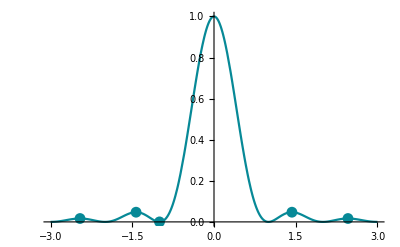

```mathematica
Show[Plot[Abs[Ex]^2 /. {a -> 1, k -> 2 π, b -> 1}, {l, -3, 3}],ListPlot[{l,Abs[Ex]^2/.{a -> 1, k -> 2 π, b -> 1}}/.pointsL]]
```

对于波长632.8nm的光，方孔尺寸0.1mm x 0.1mm，透镜焦距 100mm，在焦平面上4mm区域观察到的衍射图案，中心点的强度正比于 (a b)^2：

```mathematica
color = ColorData["VisibleSpectrum"][632.8];
condition = {l -> x/f, m -> y/f, f -> 0.1, a -> 10^-4, b -> 10^-4, k -> 2 π /λ, λ -> 632.8 10^-9};
DensityPlot[ 1/(a b)^2 Abs[Exy]^2 //. condition, {x, -0.002, 0.002}, {y, -0.002, 0.002}, PlotPoints -> 200, ColorFunction -> (Darker[color, 1 - #] &), PlotRange -> All, ColorFunctionScaling -> False
 ]
```

-Graphics-

150倍增强之后可以看到方孔衍射的典型图案：

```mathematica
color = ColorData["VisibleSpectrum"][632.8];
condition = {l -> x/f, m -> y/f, f -> 0.1, a -> 10^-4, b -> 10^-4, k -> 2 π /λ, λ -> 632.8 10^-9};
DensityPlot[ 150 /(a b)^2 Abs[Exy]^2 //. condition, {x, -0.002, 0.002}, {y, -0.002, 0.002}, PlotPoints -> 200, ColorFunction -> (Darker[color, 1 - #] &), PlotRange -> All, ColorFunctionScaling -> False
 ]
```

-Graphics-

如果方孔尺寸变为0.1mm x 0.2mm，那么y方向衍射级次间距减小：

```mathematica
color = ColorData["VisibleSpectrum"][632.8];
condition = {l -> x/f, m -> y/f, f -> 0.1, a -> 10^-4, b -> 2 10^-4, k -> 2 π /λ, λ -> 632.8 10^-9};
DensityPlot[1.5 10^18 Abs[Exy]^2 //. condition, {x, -0.002, 0.002}, {y, -0.002, 0.002}, PlotPoints -> 200, ColorFunction -> (Darker[color, 1 - #] &), PlotRange -> All, ColorFunctionScaling -> False
 ]
```

-Graphics-